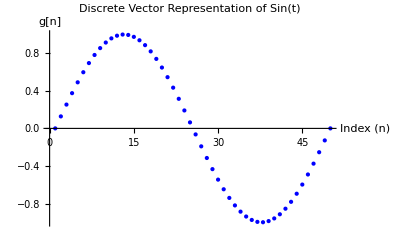

```mathematica
(*1. Define the interval and the number of sample points (N)*)a=0;
b=2*Pi;
Npoints=50;

(*Calculate the step size epsilon*)
epsilon=(b-a)/(Npoints-1);

(*2. Create the time vector by sampling the interval*)
tValues=Table[t,{t,a,b,epsilon}];

(*3. Evaluate the continuous function to create the signal vector*)
gVector=Sin[tValues];

(*4. Visualize the discrete vector data*)
ListPlot[gVector,PlotStyle->{PointSize[Large],Blue},AxesLabel->{"Index (n)","g[n]"},PlotLabel->"Discrete Vector Representation of Sin(t)"]
```

```mathematica
(*1. Continuous approach:Evaluate the inner product integral*)continuousInnerProduct=Integrate[Sin[t]*Cos[t],{t,0,2*Pi}]
Print["Continuous Inner Product: ",continuousInnerProduct];

(*2. Discrete approach:Create a second vector for Cos(t)*)
xVector=Cos[tValues];

(*Calculate the dot product of the two vectors*)
(*Note:We multiply by epsilon to approximate the integral area*)
discreteInnerProduct=Dot[gVector,xVector]*epsilon;
Print["Discrete Inner Product (approx): ",discreteInnerProduct];
(*The discrete inner product should be extremely close to 0*)
```

0

Continuous Inner Product: 0

Discrete Inner Product (approx): 0

Optimum coefficient c = 0

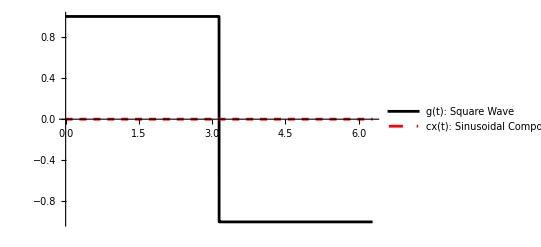

```mathematica
(*1. Define the square wave signal and the basis signal over[0,2Pi]*)gSignal[t_]:=Sign[Sin[t]];
xSignal[t_]:=Cos[t];

(*2. Calculate the energy of the basis signal Ex*)
Ex=Integrate[xSignal[t]^2,{t,0,2*Pi}];

(*3. Calculate the optimum projection coefficient c*)
c=(1/Ex)*Integrate[gSignal[t]*xSignal[t],{t,0,2*Pi}];
Print["Optimum coefficient c = ",c];
(*The output should yield 4/Pi,matching the text's derivation*)

(*4. Plot the original square wave and its sinusoidal component*)
Plot[{gSignal[t],c*xSignal[t]},{t,0,2*Pi},PlotStyle->{Black,{Red,Dashed}},PlotLegends->{"g(t): Square Wave","cx(t): Sinusoidal Component"},Exclusions->None]
```